```mathematica
transform1 = {x->r Cos[θ], y->r Sin[θ]};
d=x^2+y^2<4;
range1 = {r, 0, 3};
range2 = {θ, 0, 2 π};
range3 = {x, -3, 3};
range4 = {y, -3, 3};
```

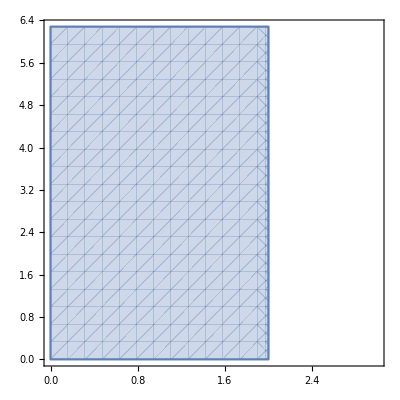

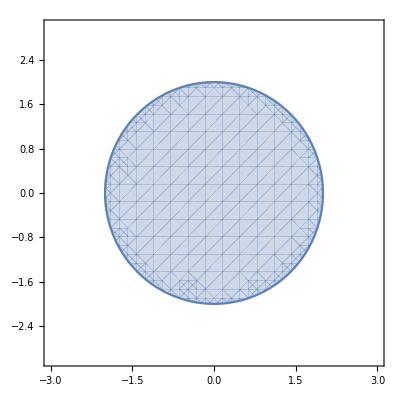

```mathematica
RegionPlot[d /. transform1, {r, range1[[2]], range1[[3]]}, {θ, range2[[2]], range2[[3]]}]
RegionPlot[d, {x, range3[[2]], range3[[3]]}, {y, range4[[2]], range4[[3]]}]
```

```mathematica
transform2[v_] := {v[[1]] Cos[v[[2]]], v[[1]] Sin[v[[2]]]};
paths = Table[{r, 2π*t}, {r, 0, 4, 1}];
tmin = 0;
tmax = 1;
```

```mathematica
Animate[Show[ParametricPlot[#* rt  + transform2[#] * (1-rt), {t, tmin, tmax}]&/@paths], {rt, 0, 1}]
```